```mathematica
Ln=4;
```

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

Ordered Entropy

```mathematica
EN[L_,p_]:=-(Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

Cyclic Entropy

```mathematica
ENC[p_]:=-(Log[1-p]+p/(1-p)*Log[p])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

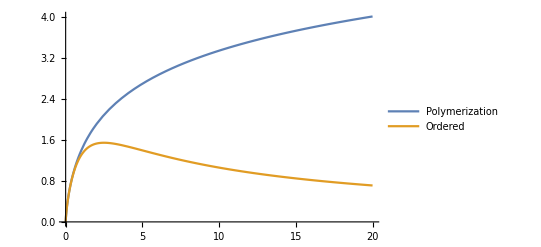

```mathematica
Plot[{ENC[h[τ]],EN[Ln,h[τ]]}, {τ,0,20},PlotLegends->{"Polymerization","Ordered"}]
```

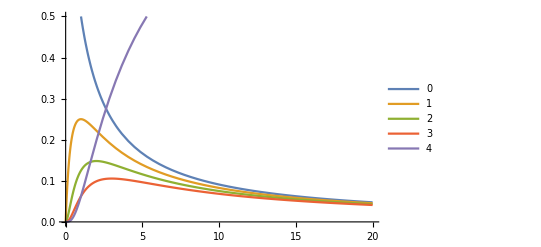

```mathematica
T=Evaluate@Table[P1[l,h[τ]],{l,0,Ln-1}];
Plot[{T, P2[Ln,h[τ]]},{τ,0,20},PlotRange->{0,0.5},PlotLegends->{"0" ,"1","2","3","4"}]
```

```mathematica
T2=Evaluate@Table[τ/.Solve[P1[i,h[τ]]==1/20&& τ>0],{i,0,Ln+1}]
```

{{19},{9-4 √5,9+4 √5},{Root[1+3 #1-17 #1^2+#1^3&,2],Root[1+3 #1-17 #1^2+#1^3&,3]},{Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,1],Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,2]},{Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2],Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]},{Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,1],Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,2]}}

```mathematica
L1=τ/.Solve[P2[Ln,h[τ]]==1/20&&τ>0]
```

{Root[-1-4 #1-6 #1^2-4 #1^3+19 #1^4&,2]}

```mathematica
a[x_]:=1/;L1[[1]]<x
b[x_]:=0.2/; x<T2[[1]]
c[x_]:=0.4/;T2[[2]][[1]]<x<T2[[2]][[1]]
d[x_]:=0.6/;T2[[3]][[1]]<x<T2[[3]][[2]]
e[x_]:=0.8/;T2[[4]][[1]]<x<T2[[4]][[1]]
f[x_]:=1/;T2[[5]][[1]]<x<T2[[5]][[2]]
g[x_]:=1.2/;T2[[6]][[1]]<x<T2[[6]][[2]]
```

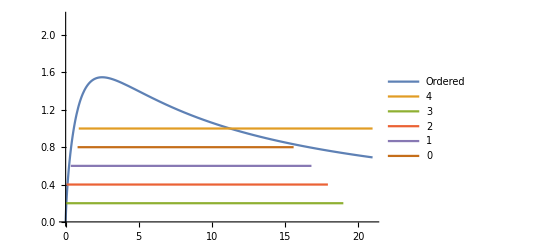

```mathematica
Plot[{EN[Ln,h[x]],a[x],b[x],c[x],d[x],e[x]},{x,0,21},PlotRange->{0,2.2},PlotLegends->{"Ordered","4","3","2","1","0"}]
```

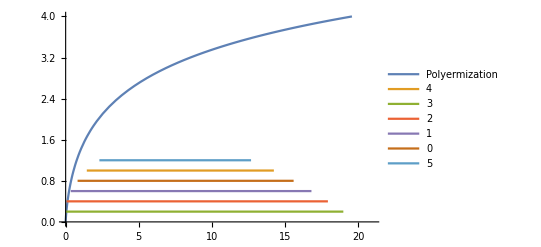

```mathematica
Plot[{ENC[h[x]],f[x],b[x],c[x],d[x],e[x],g[x]},{x,0,21},PlotRange->{0,4},PlotLegends->{"Polyermization","4","3","2","1","0","5"}]
```